# Supporting Mathematica notebook for “Patterns of speciation and parallel genetic evolution under adaptation from standing variation”

## Ken Thompson, Matthew Osmond, Dolph Schluter

Biodiversity Research Centre and Department of Zoology, University of British Columbia

## Fraction of (non)overlap

Here we are interested in the volume of the intersection between two m-dimensional spheres, with centres at distance D from one another, with radii R1 and R2. We follow Matt’s answer at https://math.stackexchange.com/questions/162250/how-to-compute-the-volume-of-intersection-between-two-hyperspheres.

The volume of the intersection is the volume of two hyperspherical caps, glued at a hyperplane.

The heights of the cap bases are

```mathematica
c1[D_,R1_,R2_]:=(D^2+R1^2-R2^2)/(2D)
c2[D_,R1_,R2_]:=(D^2-R1^2+R2^2)/(2D)
```

Computing the volume of these caps requires some fancy integration (Li 2001. Concise Formulas for the Area and Volume of a Hyperspherical Cap. Asian Journal of Mathematics and Statistics 4:66-70). It turns out the volume of a cap can be written

```mathematica
V[m_,R_,c_]:=If[c≥0,1/2 π^(m/2)/Gamma[m/2+1] R^m BetaRegularized[1-c^2/R^2,(m+1)/2,1/2],π^(m/2)/Gamma[m/2+1] R^m-1/2 π^(m/2)/Gamma[m/2+1] R^m BetaRegularized[1-c^2/R^2,(m+1)/2,1/2]]
```

where m is the dimension, R is the radius of the hypersphere, and c is the height of the cap base.

The volume of the intersection is then the sum of the volume of each cap

```mathematica
Vint=V[m,R1,c1[D,R1,R2]]+V[m,R2,c2[D,R1,R2]];
```

In our case both hyperspheres initially have the same radii, R1=R2=d, as both optima are distance d from the mean ancestral phenotype.  The distance between the centres of the hyperspheres depends on that radius and the angle between the optima (which we can restrict between 0 and 180 degress because 180 to 360 degrees is just the same thing reflected)

```mathematica
VintUs=Simplify[Vint/.R1->d/.R2->d/.D->d √(2(1-Cos[θ])),{d>0,m>0,0≤θ≤π}]
```

(d^m π^(m/2) BetaRegularized[Cos[θ/2]^2,(1+m)/2,1/2])/Gamma[1+m/2]

It looks like things are working (check areas/volumes of circle/sphere)

```mathematica
VintUs/.θ->0/.m->{2,3}
```

{d^2 π,(4 d^3 π)/3}

(note that here d is the distance to the optima, which is the radius of a hypersphere, not the diameter).

Another check: no overlap if angle is 180 degrees (for any radius or dimension)

```mathematica
Simplify[VintUs/.θ->π,{d>0,m>0}]
```

0

Then the fraction overlap is

```mathematica
Vfraction=Simplify[VintUs/(VintUs/.θ->0),m≥1]
```

BetaRegularized[Cos[θ/2]^2,(1+m)/2,1/2]

which is independent of d.

Plot the fraction overlap as a function of the angle of divergence, for many dimensions

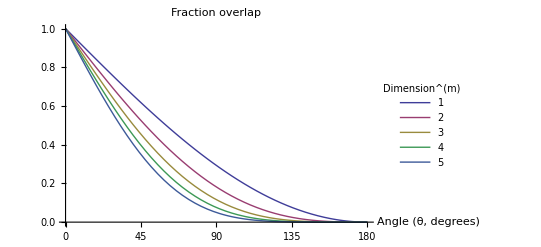

```mathematica
nms=5;
Plot[Evaluate@Table[Vfraction/.θ->θ π/180,{m,1,nms}],
{θ,0,180},
PlotLegends->Placed[LineLegend[Table[m,{m,1,nms}],LegendLabel->"Dimension^(m)"],Scaled@{0.85,0.6}],
Ticks->{{0,45,90,135,180},Automatic},
AxesLabel->{"Angle (θ, degrees)"},
PlotLabel->"Fraction overlap"]
```

Note that the fraction overlap decays faster than linearly, and fastest at highest dimension.

Plot again for even higher dimensions

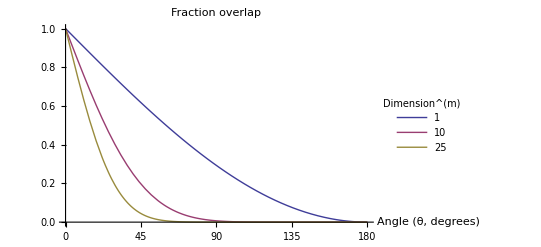

```mathematica
Plot[Evaluate@Table[Vfraction/.θ->θ π/180,{m,{1,10,25}}],
{θ,0,180},
PlotLegends->Placed[LineLegend[Table[m,{m,{1,10,25}}],LegendLabel->"Dimension^(m)"],Scaled@{0.85,0.6}],
Ticks->{{0,45,90,135,180},Automatic},
AxesLabel->{"Angle (θ, degrees)"},
PlotLabel->"Fraction overlap"]
```

Solve for angle as a function of distance between hypersphere centres (optima)

```mathematica
sol=Solve[x==d √(2(1-Cos[θ])),θ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ→-ArcCos[(2 d^2-x^2)/(2 d^2)]},{θ→ArcCos[(2 d^2-x^2)/(2 d^2)]}}

and plot the fraction overlap as function of the distance between optima

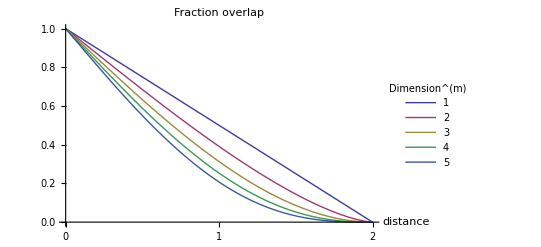

```mathematica
nms=5;
Plot[Evaluate@Table[Vfraction/.sol[[2]]/.d->1,{m,1,nms}],
{x,0,2},
PlotLegends->Placed[LineLegend[Table[m,{m,1,nms}],LegendLabel->"Dimension^(m)"],Scaled@{0.85,0.6}],
Ticks->{{0,1,2},Automatic},
AxesLabel->{"distance"},
PlotLabel->"Fraction overlap"]
```

Again the fraction overlap decays faster than linearly, with m>1, and fastest at highest dimension.

Plot this again with even higher dimensions

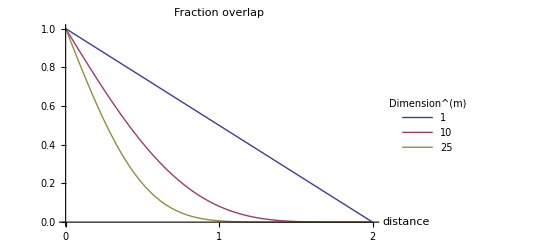

```mathematica
Plot[Evaluate@Table[Vfraction/.θ->ArcCos[(2 d^2-x^2)/(2 d^2)]/.d->1,{m,{1,10,25}}],
{x,0,2},
PlotLegends->Placed[LineLegend[Table[m,{m,{1,10,25}}],LegendLabel->"Dimension^(m)"],Scaled@{0.85,0.6}],
Ticks->{{0,1,2},Automatic},
AxesLabel->{"distance"},
PlotLabel->"Fraction overlap"]
```

As explained in the appendix, we can interpret the fraction of overlap as the fraction of beneficial mutations that are mutually beneficial for both parental populations throughout the adaptive walk towards the respective optima when we envision adaptation not as the movement of the mean parental phenotypes but as the movement of the optima. Assuming both populations adapt at the same rate, we can use the calculations above to say what the fraction of overlap is when populations have adapted a fraction f of the way to their optima. To do this we just set d = d (1-f). And because the fraction of overlap does not depend on d, it therefore remains the same over the entire adaptive walk (assuming both populations move directly towards their optima at the same rate; variation in the walks will cause this result to be an approximation). One way to understand this is to realize that as populations approach their optima the radii of the hyperspheres declines, and this decline equally reduces the space of beneficial mutations (the volume of a hypersphere) and the space of mutually beneficial mutations (the volume of the two hyperspherical caps).

## Segregation load vs. hybrid fitness

Assume the distribution of hybrid phenotypes is mutlivariate normal, centered between the two parental optima, with variance λ in each dimension, and no covariance

```mathematica
m=2;(*dimensions*)
mean=Table[(θ1[i]+θ2[i])/2,{i,1,m}];(*mean phenotype, where θj[i] is the optimum value for trait i in parent j's environment*)
covarmat=λ IdentityMatrix[m];(*variance-covariance matrix*)
vars=Table[z[i],{i,1,m}];(*m phenotypes*)
p=PDF[MultinormalDistribution[mean,covarmat],vars];(*probabily density function of hybrid phenotypes*)
```

The fitness functions in each parental environment are

```mathematica
opt1=Table[θ1[i],{i,1,m}]; (*optimum for parent 1*)
opt2=Table[θ2[i],{i,1,m}]; (*optimum for parent 2*)
w1=2 π PDF[MultinormalDistribution[opt1,IdentityMatrix[m]],vars] ;(*fitness of trait z in parent 1 environment*)
w2=2 π PDF[MultinormalDistribution[opt2,IdentityMatrix[m]],vars] ;(*fitness of trait z in parent 2 environment*)
```

Generate a vector to use in the plot function below (can’t figure out how to remove outside curly brackets, so just copy and paste without them into NIntegrate below :()

```mathematica
Table[{z[i],-2,2},{i,1,m}]
```

{{z[1],-2,2},{z[2],-2,2}}

Let the fitness of a hybrid be the maximum of fitness in the two parental environments. We then plot the mean fitness of hybrids with phenotypic variance λ in each dimension divided by the mean fitness of hybrids with no variance (λ->0) as a function of λ for three different angles of divergence

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

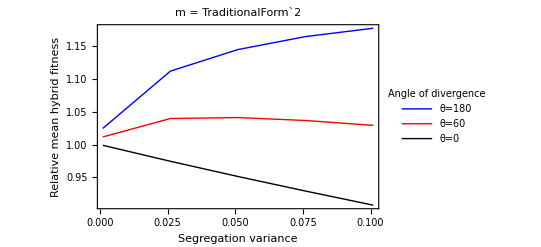

```mathematica
colors={Directive[Thick,Blue],Directive[Thick,Red],Directive[Thick,Black]};
legend={"θ=180","θ=60","θ=0"};
θ1[1]=1;
Table[θ1[i]=0,{i,2,m}];
θ2[1]=Cos[θ*π/180];
θ2[2]=Sin[θ*π/180];
Table[θ2[i]=0,{i,3,m}];
θs={180,60,0};nθ=Length[θs];

novar=(w1/.z[i_]->(θ1[i]+θ2[i])/2);

Table[{λ,NIntegrate[Max[w1,w2]p/.θ->θs[[i]],{z[1],-2,2},{z[2],-2,2},MinRecursion->50,MaxRecursion->100,Method->{GlobalAdaptive,MaxErrorIncreases->10000}]/novar/.θ->θs[[i]]},{i,Length[θs]},{λ,10^-3,0.11,0.025}];
ListPlot[%,Joined->True,PlotRange->All,Frame->{True,True,False,False},FrameLabel->{Style["Segregation variance",16],Style["Relative mean hybrid fitness",16]},PlotStyle->colors,PlotLegends->Placed[LineLegend[colors,legend,LegendLabel->"Angle of divergence"],Right],FrameStyle->Directive[FontSize->16],PlotLabel->Style[StringForm["m = ``",m],16]]
Export[NotebookDirectory[]<>"loadfit_m2.pdf",%];

Clear[θ1,θ2,θs,θ]
```

For higher dimension

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

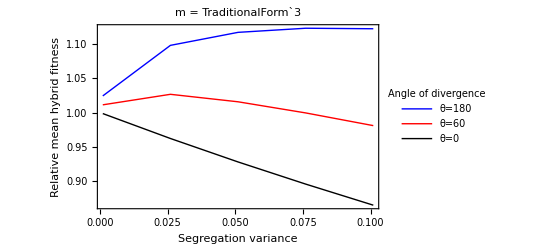

```mathematica
m=3;(*dimensions*)
mean=Table[(θ1[i]+θ2[i])/2,{i,1,m}];(*mean phenotype, where θj[i] is the optimum value for trait i in parent j's environment*)
covarmat=λ IdentityMatrix[m];(*variance-covariance matrix*)
vars=Table[z[i],{i,1,m}];(*m phenotypes*)
p=PDF[MultinormalDistribution[mean,covarmat],vars];(*probabily density function of hybrid phenotypes*)

opt1=Table[θ1[i],{i,1,m}]; (*optimum for parent 1*)
opt2=Table[θ2[i],{i,1,m}]; (*optimum for parent 2*)
w1=2 π PDF[MultinormalDistribution[opt1,IdentityMatrix[m]],vars] ;(*fitness of trait z in parent 1 environment*)
w2=2 π PDF[MultinormalDistribution[opt2,IdentityMatrix[m]],vars] ;(*fitness of trait z in parent 2 environment*)

colors={Directive[Thick,Blue],Directive[Thick,Red],Directive[Thick,Black]};
legend={"θ=180","θ=60","θ=0"};
θ1[1]=1;
Table[θ1[i]=0,{i,2,m}];
θ2[1]=Cos[θ*π/180];
θ2[2]=Sin[θ*π/180];
Table[θ2[i]=0,{i,3,m}];
θs={180,60,0};nθ=Length[θs];

novar=(w1/.z[i_]->(θ1[i]+θ2[i])/2);

Table[{λ,NIntegrate[Max[w1,w2]p/.θ->θs[[i]],{z[1],-2,2},{z[2],-2,2},{z[3],-2,2},MinRecursion->50,MaxRecursion->100,Method->{GlobalAdaptive,MaxErrorIncreases->10000}]/novar/.θ->θs[[i]]},{i,Length[θs]},{λ,10^-3,0.11,0.025}];
ListPlot[%,Joined->True,PlotRange->All,Frame->{True,True,False,False},FrameLabel->{Style["Segregation variance",16],Style["Relative mean hybrid fitness",16]},PlotStyle->colors,PlotLegends->Placed[LineLegend[colors,legend,LegendLabel->"Angle of divergence"],Right],FrameStyle->Directive[FontSize->16],PlotLabel->Style[StringForm["m = ``",m],16]]
Export[NotebookDirectory[]<>"loadfit_m3.pdf",%];

Clear[θ1,θ2,θs,θ]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0988181 and 1.58971×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.141958 and 5.37679×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.14234 and 4.65203×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

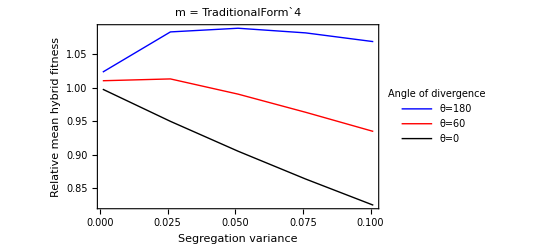

```mathematica
m=4;(*dimensions*)
mean=Table[(θ1[i]+θ2[i])/2,{i,1,m}];(*mean phenotype, where θj[i] is the optimum value for trait i in parent j's environment*)
covarmat=λ IdentityMatrix[m];(*variance-covariance matrix*)
vars=Table[z[i],{i,1,m}];(*m phenotypes*)
p=PDF[MultinormalDistribution[mean,covarmat],vars];(*probabily density function of hybrid phenotypes*)

opt1=Table[θ1[i],{i,1,m}]; (*optimum for parent 1*)
opt2=Table[θ2[i],{i,1,m}]; (*optimum for parent 2*)
w1=2 π PDF[MultinormalDistribution[opt1,IdentityMatrix[m]],vars] ;(*fitness of trait z in parent 1 environment*)
w2=2 π PDF[MultinormalDistribution[opt2,IdentityMatrix[m]],vars] ;(*fitness of trait z in parent 2 environment*)

colors={Directive[Thick,Blue],Directive[Thick,Red],Directive[Thick,Black]};
legend={"θ=180","θ=60","θ=0"};
θ1[1]=1;
Table[θ1[i]=0,{i,2,m}];
θ2[1]=Cos[θ*π/180];
θ2[2]=Sin[θ*π/180];
Table[θ2[i]=0,{i,3,m}];
θs={180,60,0};nθ=Length[θs];

novar=(w1/.z[i_]->(θ1[i]+θ2[i])/2);

Table[{λ,NIntegrate[Max[w1,w2]p/.θ->θs[[i]],{z[1],-2,2},{z[2],-2,2},{z[3],-2,2},{z[4],-2,2},MinRecursion->50,MaxRecursion->100,Method->{GlobalAdaptive,MaxErrorIncreases->10000}]/novar/.θ->θs[[i]]},{i,Length[θs]},{λ,10^-3,0.11,0.025}];
ListPlot[%,Joined->True,PlotRange->All,Frame->{True,True,False,False},FrameLabel->{Style["Segregation variance",16],Style["Relative mean hybrid fitness",16]},PlotStyle->colors,PlotLegends->Placed[LineLegend[colors,legend,LegendLabel->"Angle of divergence"],Right],FrameStyle->Directive[FontSize->16],PlotLabel->Style[StringForm["m = ``",m],16]]
Export[NotebookDirectory[]<>"loadfit_m4.pdf",%];

Clear[θ1,θ2,θs,θ]
```

Note that under parallel selection (θ=0), segregation variance is always bad as then the mean hybrid phenotype is on the two optima, and any variance is a load. Under less parallel selection (θ=60,180), some segregation variance can increase mean fitness, as then some individuals are closer to the parental optima. But as the dimension increases this benefit of variation wanes because there are more ways to go wrong (away from the parental optima) then to go right (towards the parental optima).